## Lesson

Show the compiler form of an expression:

```mathematica
FullForm[a+b c]
```

Plus[a,Times[b,c]]

Make a tree of the compiler form:

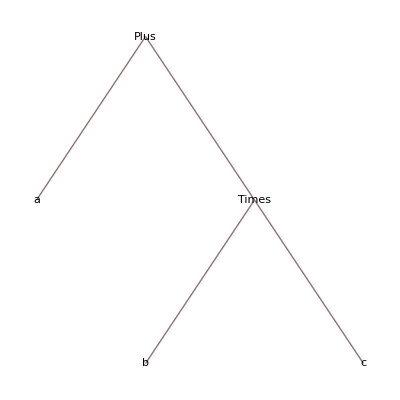

```mathematica
TreeForm[a+b c]
```

Extract the head (root of tree form):

```mathematica
Head[a+b c]
```

Plus

Match any expression with a particular head:

```mathematica
Cases[_Integer]@Select[#>4&]@{1,2.2,3,4.5,5,6,7.5,8}
```

{5,6,8}

Replace the head of list with function (apply):

```mathematica
Rule@@{x,y}
```

x→y

Replace the heads of lists with function (map apply):

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

Note that mapping does not care about the head at all:

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

## Questions

Q1. Find the head of the output from ListPlot.

```mathematica
Head[ListPlot[Range[5]]]
```

Graphics

Q2. Use @@ to compute the result of multiplying together integers up to 100.

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

Q3. Use @@@ and Tuples to generate {f[a, a], f[a, b], f[b, a], f[b, b]}.

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

Q4. Make a list of tree forms for the results of 4 successive applications of #^#& starting from x.

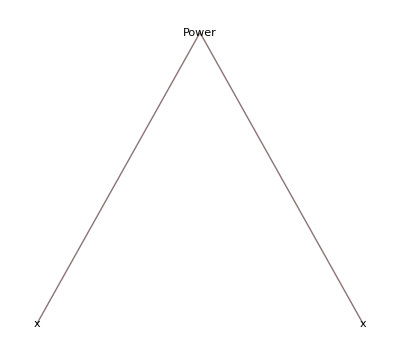
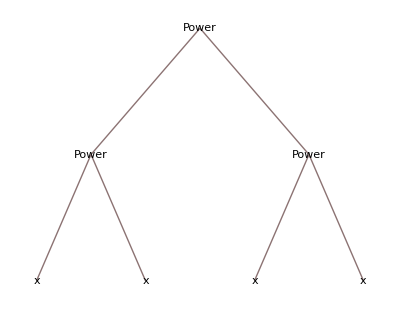
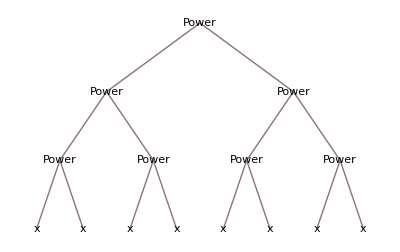
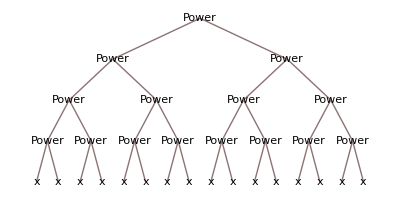
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TreeForm/@NestList[#^#&,x,4]
```

Q5. Find the unique cases where i^2/(j^2+1) is an integer, with i and j going up to 20.

```mathematica
Union[Cases[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

Q6. Create a graph that connects successive pairs of numbers in Table[Mod[n^2+n, 100], {n, 100}].

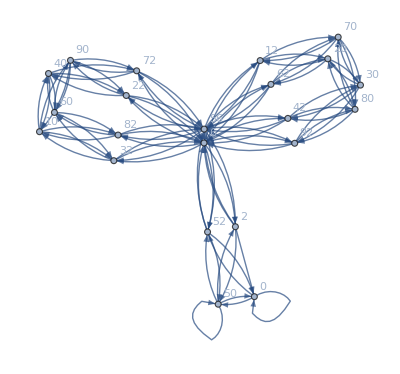

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1],VertexLabels->Automatic]
```

Q7. Generate a graph showing which word can follow which in the first 200 words of the Wikipedia article on computers.

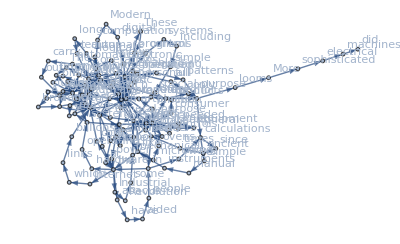

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["computers"],200],2,1],VertexLabels->Automatic]
```

Q8. Find a simpler form for f@@#&/@{{1, 2}, {7, 2}, {5, 4}}.

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}